```mathematica
(*Зададим данную функцию и построим ее график*)
f[x_,y_]=3*x^2*y+y^3-12*x-15*y+3;
Plot3D[f[x,y],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
(*Локализуем точку максимума данной функции*)
G=Plot3D[f[x,y],{x,-2,0},{y,-3,-1}]
```

-Graphics3D-

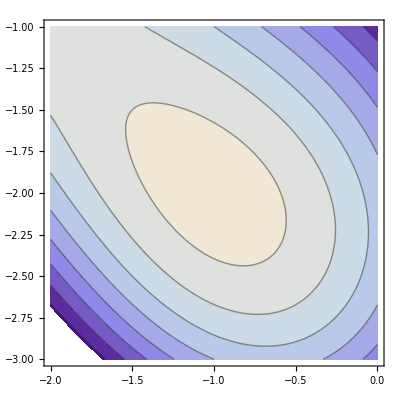

```mathematica
(*Построим линии уровня данной функции*)
GC=ContourPlot[f[x,y],{x,-2,0},{y,-3,-1}]
```

```mathematica
(*Перейдем к противоположной функции, так как ищется точка максимума*)
g[x_,y_]=-f[x,y];
(*Найдем нормированный градиент функции g[x,y]*)
n[x_,y_]=Grad[g[x,y],{x,y}]/Norm[Grad[g[x,y],{x,y}]];
(*Зададим точность вычислений*)
eps=10^(-5);
(*Зададим начальное приближение к точке экстремума*)
M0={0,-3};
(*Зададим шаг приближения*)
lambda=1;
(*Зададим счетчик итераций*)
k=0;
(*Построим последовательность приближений к точке максимума*)
IT={Join[M0,{f[M0[[1]],M0[[2]]]}]};
(*Реализуем алгоритм градиентного метода поиска экстремума*)
While[lambda≥eps,
M1=M0-lambda*N[n[M0[[1]],M0[[2]]]];
If[g[M1[[1]],M1[[2]]]<g[M0[[1]],M0[[2]]],
M0=M1;
k=k+1;
AppendTo[IT,Join[M1,{f[M1[[1]],M1[[2]]]}]],
lambda=lambda/2
]
];
M1=M0-lambda*N[n[M0[[1]],M0[[2]]]];
k=k+1;
AppendTo[IT,Join[M1,{f[M1[[1]],M1[[2]]]}]];
Print["Точка максимума функции равна: ",M1]
Print["Значение функции в точке максимума равно: ",f[M1[[1]],M1[[2]]]]
Print["Количество итераций равно: ",k]
```

Точка максимума функции равна: {-0.999996,-2.}

Значение функции в точке максимума равно: 31.

Количество итераций равно: 11

```mathematica
Animate[Show[G,ListPointPlot3D[{IT[[i]]},PlotStyle->Red]],{i,1,k+1,1},AnimationRunning->False]
```

```mathematica
Animate[Show[GC,ListPlot[{{IT[[i,1]],IT[[i,2]]}},PlotStyle->Red]],{i,1,k+1,1},AnimationRunning->False]
```